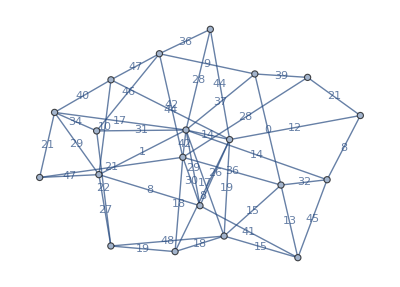

```mathematica
G=RandomGraph[{20,48},EdgeWeight->RandomInteger[48,48],EdgeLabels->"EdgeWeight"]
```

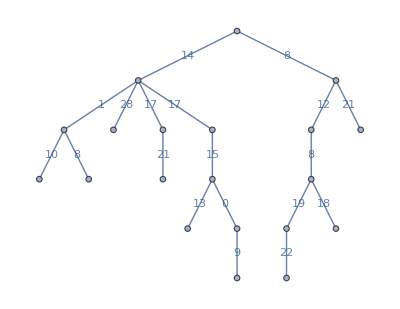

```mathematica
MST=FindSpanningTree[G]
```

```mathematica
oddVertices=Select[VertexList[MST],OddQ[VertexDegree[MST,#]]&]
```

{1,2,3,4,5,6,8,9,10,12,13,14,18,19}

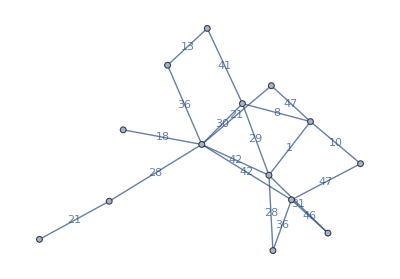

```mathematica
Subgraph[G,oddVertices]
```

```mathematica
minimumCostPerfectMatching=FindIndependentEdgeSet[Subgraph[G,oddVertices]]
```

{1<->9,2<->3,4<->6,5<->10,13<->14,18<->19}

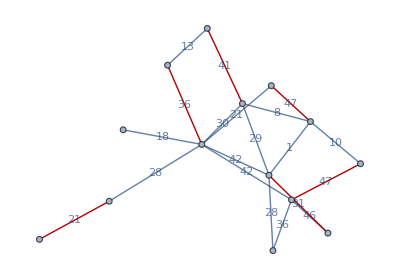

```mathematica
HighlightGraph[Subgraph[G,oddVertices],FindIndependentEdgeSet[Subgraph[G,oddVertices]]]
```

```mathematica
Flatten[EdgeList/@{MST,minimumCostPerfectMatching}]
```

{1<->5,1<->11,2<->8,3<->6,3<->18,3<->19,4<->9,4<->15,5<->8,6<->10,7<->14,7<->18,8<->18,9<->13,11<->15,12<->17,14<->17,14<->20,16<->20,1<->8,3<->10,4<->16,5<->6,7<->11,9<->13,14<->20}

```mathematica
Graph[Flatten[EdgeList/@{MST,minimumCostPerfectMatching}]]
```

-Graphics-

```mathematica
EulerianGraphQ[Graph[Flatten[EdgeList/@{MST,minimumCostPerfectMatching}]]]
```

False

```mathematica
Intersection[EdgeList/@{MST,minimumCostPerfectMatching}]
```

{{1<->8,3<->10,4<->16,5<->6,7<->11,9<->13,14<->20},{1<->5,1<->11,2<->8,3<->6,3<->18,3<->19,4<->9,4<->15,5<->8,6<->10,7<->14,7<->18,8<->18,9<->13,11<->15,12<->17,14<->17,14<->20,16<->20}}

```mathematica
AssociationMap[EulerianGraphQ@GraphProduct[MST,minimumCostPerfectMatching,#]&,{"Cartesian","Conormal","Lexicographical","Normal","Rooted","Tensor"}]
```

<|Cartesian→False,Conormal→False,Lexicographical→False,Normal→False,Rooted→False,Tensor→False|>

```mathematica
AssociationMap[EulerianGraphQ@#[MST,minimumCostPerfectMatching]&,{GraphUnion,GraphSum,GraphJoin,GraphDisjointUnion,GraphIntersection,GraphDifference}]
```

<|GraphUnion→False,GraphSum→False,GraphJoin→False,GraphDisjointUnion→False,GraphIntersection→False,GraphDifference→False|>

```mathematica
Intersection[EdgeList[MST],EdgeList[minimumCostPerfectMatching]]
```

{9<->13,14<->20}

```mathematica
Union[EdgeList[MST],EdgeList[minimumCostPerfectMatching]]
```

{1<->5,1<->8,1<->11,2<->8,3<->6,3<->10,3<->18,3<->19,4<->9,4<->15,4<->16,5<->6,5<->8,6<->10,7<->11,7<->14,7<->18,8<->18,9<->13,11<->15,12<->17,14<->17,14<->20,16<->20}

```mathematica
Graph@Join[EdgeList[MST],EdgeList[minimumCostPerfectMatching]]
```

-Graphics-

```mathematica
VertexDegree@Graph[Join[EdgeList[MST],{1<->11,3<->6,4<->9,5<->8,6<->10,7<->14,9<->13,16<->20}]]
```

{3,3,3,1,4,4,4,3,1,3,4,2,2,3,4,2,1,2,3,2}

```mathematica
Names["*Cover*"]
```

{ColorCoverage,EdgeCoverQ,FindEdgeCover,FindVertexCover,VertexCoverQ}

```mathematica
FindVertexCover[Subgraph[G,oddVertices]]
```

{1,3,4,5,7,10,13,20}

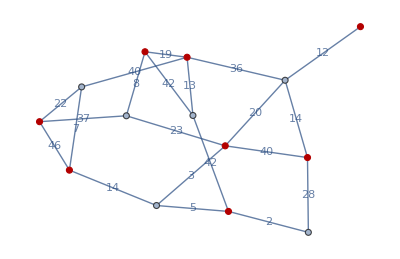

```mathematica
HighlightGraph[Graph[{1,3,4,5,6,7,8,9,10,11,13,14,16,20},{Null,SparseArray[Automatic,{14,14},0,{1,{{0,3,6,9,13,16,20,23,27,30,33,34,37,39,42},{{4},{7},{10},{5},{9},{12},{6},{8},{13},{1},{5},{7},{8},{2},{4},{9},{3},{8},{10},{12},{1},{4},{14},{3},{4},{6},{11},{2},{5},{10},{1},{6},{9},{8},{2},{6},{14},{3},{14},{7},{12},{13}}},Pattern}]},{EdgeLabels->{"EdgeWeight"},EdgeWeight->{19,42,8,7,46,14,40,14,28,40,13,36,22,20,23,3,42,12,37,5,2}}],{1,3,4,5,7,10,13,20}]
```

```mathematica
FindEdgeCover[Subgraph[G,oddVertices]]
```

{1<->11,3<->6,4<->9,5<->8,6<->10,7<->14,9<->13,16<->20}

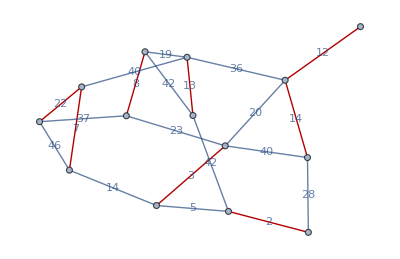

```mathematica
HighlightGraph[Graph[{1,3,4,5,6,7,8,9,10,11,13,14,16,20},{Null,SparseArray[Automatic,{14,14},0,{1,{{0,3,6,9,13,16,20,23,27,30,33,34,37,39,42},{{4},{7},{10},{5},{9},{12},{6},{8},{13},{1},{5},{7},{8},{2},{4},{9},{3},{8},{10},{12},{1},{4},{14},{3},{4},{6},{11},{2},{5},{10},{1},{6},{9},{8},{2},{6},{14},{3},{14},{7},{12},{13}}},Pattern}]},{EdgeLabels->{"EdgeWeight"},EdgeWeight->{19,42,8,7,46,14,40,14,28,40,13,36,22,20,23,3,42,12,37,5,2}}],{1<->11,3<->6,4<->9,5<->8,6<->10,7<->14,9<->13,16<->20}]
```

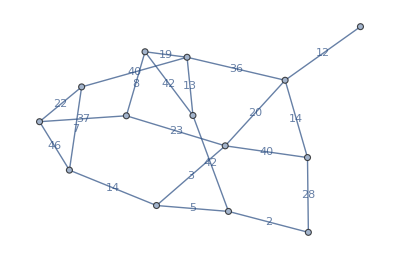

```mathematica
Subgraph[G,oddVertices]
```

```mathematica
VertexCount@Subgraph[G,oddVertices]
```

14

```mathematica
Join[EdgeList@FindIndependentEdgeSet[Subgraph[G,oddVertices]],EdgeList@MST]
```

{1<->8,3<->10,4<->16,5<->6,7<->11,9<->13,14<->20,1<->5,1<->11,2<->8,3<->6,3<->18,3<->19,4<->9,4<->15,5<->8,6<->10,7<->14,7<->18,8<->18,9<->13,11<->15,12<->17,14<->17,14<->20,16<->20}

```mathematica
Graph@Join[EdgeList@FindIndependentEdgeSet[Subgraph[G,oddVertices]],EdgeList@MST]
```

-Graphics-

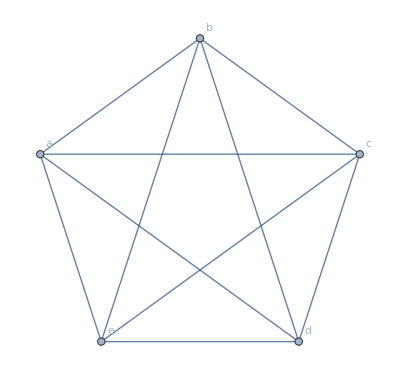

```mathematica
Graph[{a,b,c,d,e},{a<->b,b<->c,c<->d,d<->a,a<->e,a<->c,b<->e,c<->e,d<->e,b<->d},VertexLabels->Automatic]
```

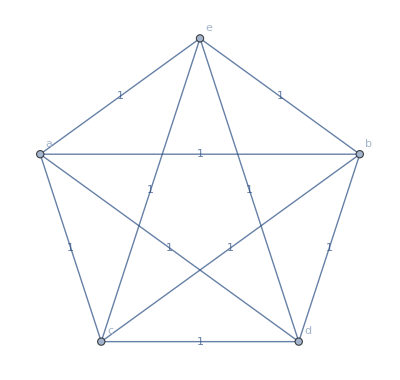

```mathematica
G=Graph[UndirectedEdge@@@{{a,e,2},{a,b,1},{a,d,1},{a,c,1},{b,e,1},{b,c,1},{b,d,2},{e,c,1},{d,e,1},{d,c,1}},EdgeLabels->"EdgeWeight",VertexLabels->Automatic]
```

```mathematica
UndirectedEdge@@@{{a,e,2},{a,b,1},{a,d,1},{a,c,1},{b,e,1},{b,c,1},{b,d,2},{e,c,1},{d,e,1},{d,c,1}}
```

{ae2,ab1,ad1,ac1,be1,bc1,bd2,ec1,de1,dc1}

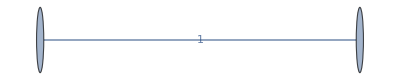

```mathematica
Graph[{a,e},{ae2},EdgeLabels->"EdgeWeight"]
```

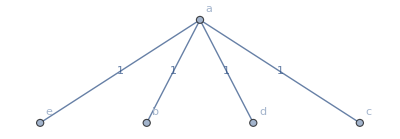

```mathematica
minimumSpanningTree=FindSpanningTree[G]
```

```mathematica
Select[VertexList[]]
```

```mathematica
G=RandomGraph[{20,48},EdgeWeight->RandomInteger[48,48],EdgeLabels->"EdgeWeight"]
```

-Graphics-

```mathematica
T=FindSpanningTree[G]
```

-Graphics-

```mathematica
oddVertices=Select[VertexList[T],OddQ[VertexDegree[T,#]]&]
```

{1,2,3,4,5,6,8,9,10,12,13,14,18,19}

```mathematica
FindIndependentEdgeSet@Subgraph[G,oddVertices]
```

{1<->9,2<->3,4<->6,5<->10,13<->14,18<->19}

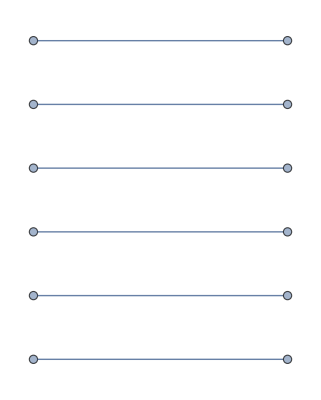

```mathematica
minimumCostPerfectMatching=Graph@FindIndependentEdgeSet[Subgraph[G,oddVertices]]
```

```mathematica
Join[EdgeList[MST],FindIndependentEdgeSet@Subgraph[G,oddVertices]]
```

{1<->20,2<->15,3<->6,3<->9,3<->10,4<->11,5<->18,6<->8,6<->15,6<->16,6<->17,7<->12,7<->13,11<->12,12<->19,13<->14,13<->17,16<->18,18<->20,1<->9,2<->3,4<->6,5<->10,13<->14,18<->19}

```mathematica
Graph[%173]
```

-Graphics-

```mathematica
Graph[Join[EdgeList[MST],EdgeList[minimumCostPerfectMatching]]]
```

-Graphics-

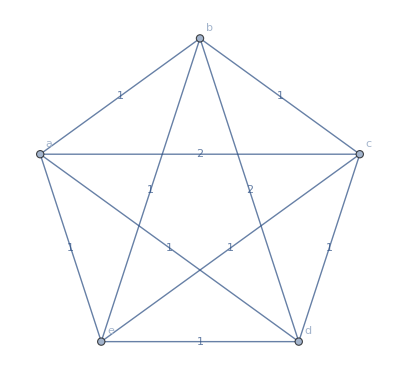

```mathematica
G=Graph[{a,b,c,d,e},{a<->b,a<->e,a<->d,a<->c,b<->c,b<->e,c<->e,c<->d,d<->e,b<->d},VertexLabels->Automatic,EdgeWeight->Thread[{a<->b,a<->e,a<->d,a<->c,b<->c,b<->e,c<->e,c<->d,d<->e,b<->d}->{1,1,1,2,1,1,1,1,1,2}],EdgeLabels->"EdgeWeight"]
```

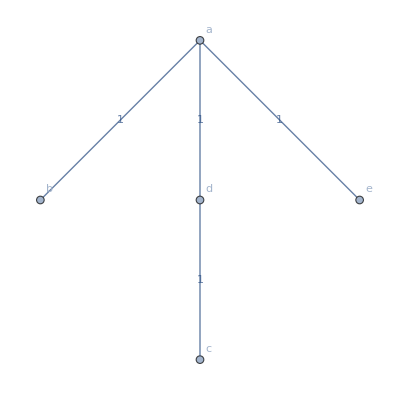

```mathematica
T=FindSpanningTree[G]
```

```mathematica
Select[VertexList[T],OddQ[VertexDegree[T,#]]&]
```

{a,b,c,e}

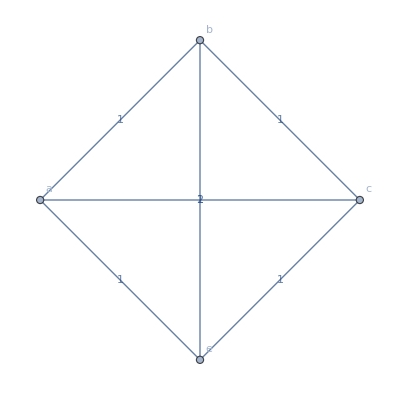

```mathematica
Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]
```

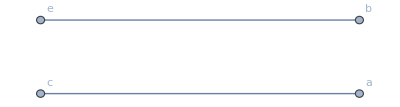

```mathematica
Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic]
```

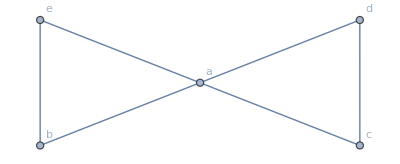

```mathematica
GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]
```

```mathematica
FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]]
```

{{a<->d,d<->c,c<->a,a<->e,e<->b,b<->a}}

```mathematica
Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]
```

{a,d,d,c,c,a,a,e,e,b,b,a}

```mathematica
DeleteDuplicates@Partition[RotateRight[Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]],2]
```

{{a,a},{d,d},{c,c},{e,e},{b,b}}

```mathematica
RotateLeft[Flatten[DeleteDuplicates@Partition[RotateRight[Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]],2]]]
```

{a,d,d,c,c,e,e,b,b,a}

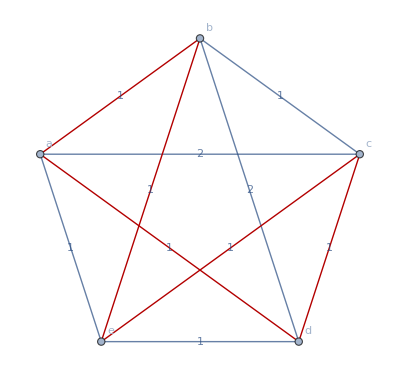

```mathematica
HighlightGraph[G,UndirectedEdge@@@Partition[RotateLeft[Flatten[DeleteDuplicates@Partition[RotateRight[Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]],2]]],2]]
```

```mathematica
HighlightGraph[G,UndirectedEdge@@@Partition[RotateLeft[Flatten[DeleteDuplicates@Partition[RotateRight[Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]],2]]],2]]
```

```mathematica
FindShortestTour[G]
```

{5,{1,2,3,4,5,1}}

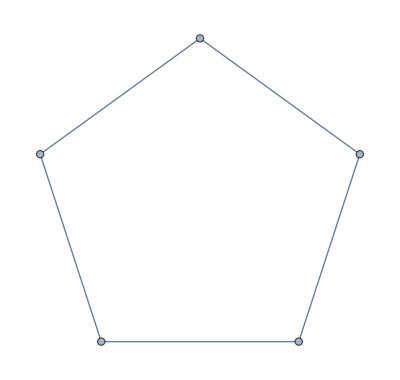

```mathematica
HighlightGraph[PathGraph[FindShortestTour[G][[2]]]
```

```mathematica
p=RandomReal[10,{50,2}];
FindShortestTour[p]
```

{56.6498,{1,33,12,35,3,14,8,31,26,48,22,20,39,11,28,49,37,25,44,42,15,29,9,13,19,7,23,41,34,21,46,43,40,16,18,4,38,5,50,6,17,47,36,32,10,45,27,2,24,30,1}}

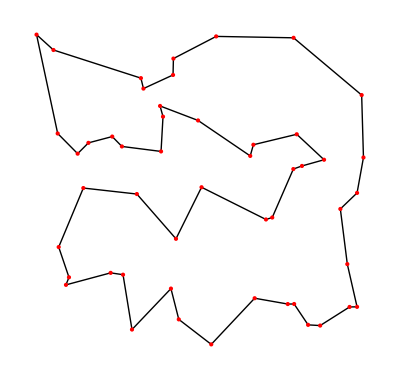

```mathematica
Graphics[{Line[p[[Last[%]]]],PointSize[Medium],Red,Point[p]}]
```

```mathematica
PrintDefinitions["FindPostmanTour"]
```

```mathematica
Unprotect["FindPostmanTour"]
```

{FindPostmanTour}

```mathematica
EdgeList[ℛ]
```

{1<->16,1<->18,1<->7,1<->14,1<->19,1<->3,2<->20,2<->13,2<->6,2<->9,2<->8,2<->10,2<->15,2<->4,3<->14,3<->16,3<->7,4<->9,4<->15,4<->12,4<->7,5<->20,6<->8,6<->13,6<->10,7<->16,7<->18,7<->14,7<->19,8<->10,8<->13,8<->17,9<->12,9<->13,9<->15,9<->10,9<->20,10<->13,10<->17,10<->12,11<->17,11<->12,12<->17,12<->13,13<->20,13<->17,14<->16,14<->18,15<->20,16<->18,16<->19,18<->19}

```mathematica
MapAt[First[#]->Last[#]&,EdgeList[ℛ],List/@RandomSample[Range[20],10]]
```

{1<->16,1<->18,1<->7,1->14,1->19,1<->3,2<->20,2<->13,2->6,2<->9,2<->8,2<->10,2->15,2<->4,3->14,3->16,3->7,4->9,4->15,4->12,4<->7,5<->20,6<->8,6<->13,6<->10,7<->16,7<->18,7<->14,7<->19,8<->10,8<->13,8<->17,9<->12,9<->13,9<->15,9<->10,9<->20,10<->13,10<->17,10<->12,11<->17,11<->12,12<->17,12<->13,13<->20,13<->17,14<->16,14<->18,15<->20,16<->18,16<->19,18<->19}

```mathematica
Transpose[{EdgeList[ℛ],MapAt[First[#]->Last[#]&,EdgeList[ℛ],List/@RandomSample[Range[20],10]]}]
```

{{1<->6,1<->6},{1<->4,1<->4},{2<->17,2->17},{2<->18,2->18},{2<->5,2<->5},{2<->11,2->11},{3<->13,3<->13},{3<->19,3<->19},{3<->16,3<->16},{3<->20,3->20},{4<->15,4->15},{4<->8,4->8},{5<->10,5<->10},{5<->17,5->17},{6<->9,6<->9},{6<->20,6->20},{7<->10,7->10},{7<->14,7<->14},{8<->14,8<->14},{9<->20,9->20},{10<->14,10<->14},{11<->12,11<->12},{13<->19,13<->19},{13<->16,13<->16},{13<->20,13<->20},{16<->19,16<->19},{16<->18,16<->18},{17<->18,17<->18},{18<->20,18<->20},{18<->19,18<->19},{19<->20,19<->20}}

```mathematica
{First@#1,Last@#2}&@@Transpose[{EdgeList[ℛ],MapAt[First[#]->Last[#]&,EdgeList[ℛ],List/@RandomSample[Range@EdgeCount[ℛ],Floor[EdgeCount[ℛ]]]]}]
```

{2<->14,2->7}

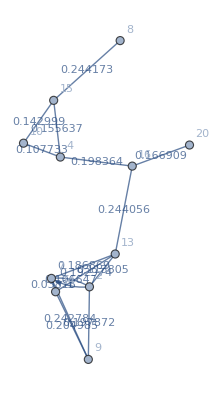

```mathematica
EdgeAdd[EdgeDelete[ℛ,First@#1],Last@#2]&@@Transpose[{EdgeList[ℛ],MapAt[First[#]->Last[#]&,EdgeList[ℛ],List/@RandomSample[Range@EdgeCount[ℛ],Floor[EdgeCount[ℛ]]]]}]
```

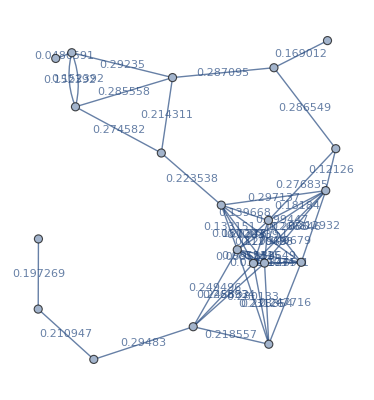
{-Graphics-,-Graphics-}

```mathematica
EdgeAdd[EdgeDelete[ℛ,#1],#2]&@@@{EdgeList[ℛ],MapAt[First[#]->Last[#]&,EdgeList[ℛ],List/@RandomSample[Range[20],10]]}
```

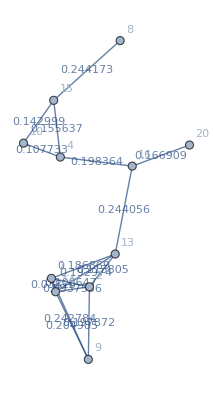

```mathematica
ℛ
```

```mathematica
EdgeList[ℛ]
```

{2<->14,2<->7,7<->14,2<->13,7<->13,13<->14,2<->9,7<->9,9<->14,13<->16,4<->16,16<->20,4<->10,4<->15,10<->15,8<->15}

```mathematica
AnnotationValue[{ℛ,#},EdgeWeight]&/@EdgeList[ℛ]
```

{0.0937556,0.106647,0.03816,0.113805,0.186869,0.192974,0.197872,0.242784,0.204985,0.244056,0.198364,0.166909,0.107733,0.155637,0.142999,0.244173}

```mathematica
RandomSample[EdgeList[ℛ],Floor[EdgeCount[ℛ]]]
```

{2<->13,10<->15,16<->20,13<->14,13<->16,9<->14,2<->9,4<->16,2<->7,7<->14,8<->15,7<->13,4<->15,4<->10,7<->9,2<->14}

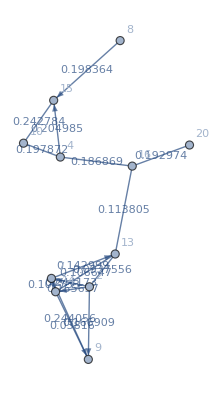

```mathematica
Graph[Fold[EdgeDelete[EdgeAdd[#1,First[#2]->Last[#2]],#2]&,ℛ,RandomSample[EdgeList[ℛ],Floor[EdgeCount[ℛ]/2]]],EdgeWeight->(AnnotationValue[{ℛ,#},EdgeWeight]&/@EdgeList[ℛ])]
```

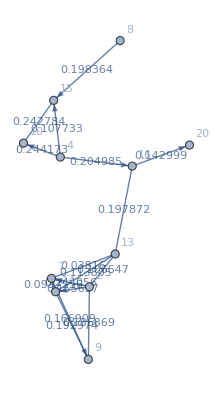

```mathematica
𝒫=Graph[Fold[EdgeDelete[EdgeAdd[#1,First[#2]->Last[#2]],#2]&,ℛ,RandomSample[EdgeList[ℛ],Floor[EdgeCount[ℛ]/2]]],EdgeWeight->(AnnotationValue[{ℛ,#},EdgeWeight]&/@EdgeList[ℛ])]
```

```mathematica
ConnectedGraphQ[𝒫]
```

False

```mathematica
EntityClass["Country", "NATO"][EntityProperty["Country", "CapitalCity"]]
```

{Tirana,Brussels,Sofia,Ottawa,Zagreb,Prague,Copenhagen,Tallinn,Paris,Berlin,Athens,Budapest,Reykjavik,Rome,Riga,Vilnius,Luxemburg,Skopje,Podgorica,Amsterdam,Oslo,Warsaw,Lisbon,Bucharest,Bratislava,Ljubljana,Madrid,Ankara,London,Washington}

```mathematica
HighlightGraph[G,UndirectedEdge@@@Partition[RotateLeft[Flatten[DeleteDuplicates@Partition[RotateRight[Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]],2]]],2]]
```

-Graphics-

```mathematica
EVENDEGREE[g_?(ConnectedGraphQ[#]∧MixedGraphQ[#]&)]:=Module[{oddVertices,shortestPathGroups},oddVertices=Select[VertexList[g],OddQ[VertexDegree[g,#]]&]]
```

```mathematica
EVENDEGREE[G]
```

{}

```mathematica
G
```

-Graphics-